```mathematica
ccOneSqr=buildCC2D[{{1}}];
```

```mathematica
p1=getNumParent[ccOneSqr]
```

{{{2,{1,4},{},False},{2,{1,2},{},False},{2,{2,3},{},False},{2,{3,4},{},False}},{{1,{1},{1,2},True},{1,{1},{2,3},False},{1,{1},{3,4},False},{1,{1},{4,1},False}},{{0,{},{1,2,3,4},True}}}

```mathematica
p1rmp=removeKilledParentIndex[p1,ccOneSqr]
```

{{{1,{4},{},False},{1,{2},{},False},{2,{2,3},{},False},{2,{3,4},{},False}},{{0,{},{},True},{0,{},{2,3},False},{0,{},{3,4},False},{0,{},{4,1},False}},{{0,{},{},True}}}

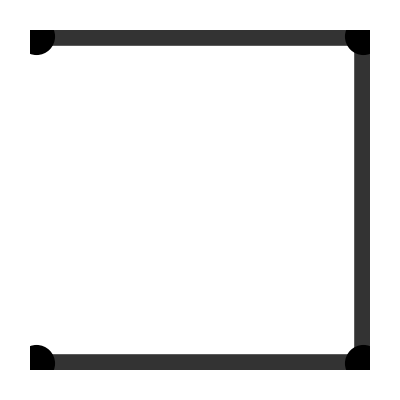

```mathematica
showCC2D[restoreAfterEThinning[p1rmp,ccOneSqr]]
```

```mathematica
{p12,sp}=updateDisjoint[p1rmp,ccOneSqr]
```

{{{{1,{4},{},True},{1,{2},{},True},{2,{2,3},{},False},{2,{3,4},{},False}},{{0,{},{},True},{0,{},{2,3},True},{0,{},{3,4},False},{0,{},{4,1},True}},{{0,{},{},True}}},2}

```mathematica
p12rmp=removeKilledParentIndex[p12,ccOneSqr]
```

{{{0,{},{},True},{0,{},{},True},{1,{3},{},False},{1,{3},{},False}},{{0,{},{},True},{0,{},{},True},{0,{},{3,4},False},{0,{},{},True}},{{0,{},{},True}}}

```mathematica
showCC2D[restoreAfterEThinning[p12rmp,ccOneSqr]]
```

Part::partw: Part {3,4} of {{3,3},{3,1}} does not exist.

-Graphics-

```mathematica
{p123,sp}=updateDisjoint[p12rmp,ccOneSqr]
```

{{{{0,{},{},True},{0,{},{},True},{1,{3},{},True},{1,{3},{},False}},{{0,{},{},True},{0,{},{},True},{0,{},{3,4},True},{0,{},{},True}},{{0,{},{},True}}},1}

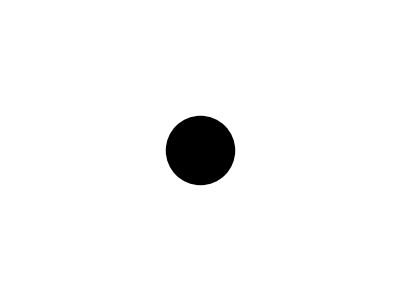

```mathematica
showCC2D[restoreAfterEThinning[p123,ccOneSqr]]
```

```mathematica
p123rmp=removeKilledParentIndex[p123,ccOneSqr]
```

{{{0,{},{},True},{0,{},{},True},{0,{},{},True},{0,{},{},False}},{{0,{},{},True},{0,{},{},True},{0,{},{},True},{0,{},{},True}},{{0,{},{},True}}}

```mathematica
{p1234,sp}=updateDisjoint[p1234,ccOneSqr]
```

{{{{0,{},{},True},{0,{},{},True},{0,{},{},True},{0,{},{},False}},{{0,{},{},True},{0,{},{},True},{0,{},{},True},{0,{},{},True}},{{0,{},{},True}}},0}

```mathematica
showCC2D[restoreAfterEThinning[p1234,ccOneSqr]]
```

-Graphics-

```mathematica
restoreAfterEThinning2[p1234,ccOneSqr]
```

{{{3,1}},{},{}}

!

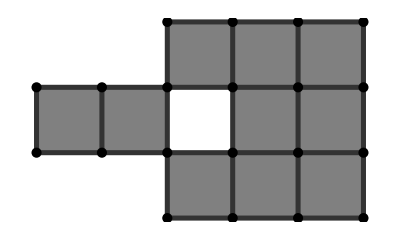

```mathematica
showCC2D[cc1]
```

```mathematica
ppp=thinExhaustive[cc1]
```

{{{0,{},{},True},{0,{},{},True},{0,{},{},True},{0,{},{},True},{2,{6,15},{},False},{2,{6,9},{},False},{0,{},{},True},{2,{9,16},{},False},{0,{},{},True},{0,{},{},True},{0,{},{},True},{2,{15,20},{},False},{2,{16,21},{},False},{0,{},{},True},{2,{20,21},{},False},{0,{},{},True},{0,{},{},True},{0,{},{},True},{0,{},{},True},{0,{},{},True}},{{0,{},{},True},{0,{},{},True},{0,{},{},True},{0,{},{},True},{0,{},{},True},{0,{},{5,6},False},{0,{},{},True},{0,{},{},True},{0,{},{6,8},False},{0,{},{},True},{0,{},{},True},{0,{},{},True},{0,{},{},True},{0,{},{},True},{0,{},{12,5},False},{0,{},{8,13},False},{0,{},{},True},{0,{},{},True},{0,{},{},True},{0,{},{12,15},False},{0,{},{15,13},False},{0,{},{},True},{0,{},{},True},{0,{},{},True},{0,{},{},True},{0,{},{},True},{0,{},{},True},{0,{},{},True},{0,{},{},True},{0,{},{},True}},{{0,{},{},True},{0,{},{},True},{0,{},{},True},{0,{},{},True},{0,{},{},True},{0,{},{},True},{0,{},{},True},{0,{},{},True},{0,{},{},True},{0,{},{},True}}}

```mathematica
restoreAfterEThinning2[ppp,cc1]
```

{{{1,-1},{2,-1},{3,-1},{4,-1},{5,1},{6,2},{7,-1},{8,3},{9,-1},{10,-1},{11,-1},{12,4},{13,5},{14,-1},{15,6},{16,-1},{17,-1},{18,-1},{19,-1},{20,-1}},{{1,-1},{2,-1},{3,-1},{4,-1},{5,-1},{6,1},{7,-1},{8,-1},{9,2},{10,-1},{11,-1},{12,-1},{13,-1},{14,-1},{15,3},{16,4},{17,-1},{18,-1},{19,-1},{20,5},{21,6},{22,-1},{23,-1},{24,-1},{25,-1},{26,-1},{27,-1},{28,-1},{29,-1},{30,-1}},{{1,-1},{2,-1},{3,-1},{4,-1},{5,-1},{6,-1},{7,-1},{8,-1},{9,-1},{10,-1}}}

Above is index Map

{{{5,5},{5,3},{7,3},{7,5},{9,3},{9,5}},{{5,6},{6,8},{12,5},{8,13},{12,15},{15,13}},{}}

Above is new CC

omg?

Set at 2th row and 1th elem's 1th comp from {5,6} to 1

Set at 2th row and 1th elem's 2th comp from {5,6} to 2

Set at 2th row and 2th elem's 1th comp from {6,8} to 2

Set at 2th row and 2th elem's 2th comp from {6,8} to 3

Set at 2th row and 3th elem's 1th comp from {12,5} to 4

Set at 2th row and 3th elem's 2th comp from {12,5} to 1

Set at 2th row and 4th elem's 1th comp from {8,13} to 3

Set at 2th row and 4th elem's 2th comp from {8,13} to 5

Set at 2th row and 5th elem's 1th comp from {12,15} to 4

Set at 2th row and 5th elem's 2th comp from {12,15} to 6

Set at 2th row and 6th elem's 1th comp from {15,13} to 6

Set at 2th row and 6th elem's 2th comp from {15,13} to 5

omg2?

{{{5,5},{5,3},{7,3},{7,5},{9,3},{9,5}},{{1,2},{2,3},{4,1},{3,5},{4,6},{6,5}},{}}

!

!

"!

{{{3,1}},{},{}}

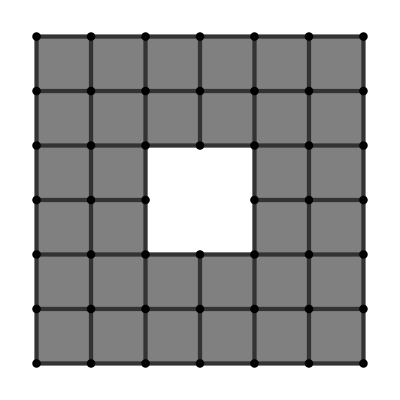

```mathematica
showCC2D[cc2]
```

{{{1,-1},{2,-1},{3,-1},{4,-1},{5,-1},{6,1},{7,-1},{8,2},{9,-1},{10,3},{11,-1},{12,-1},{13,-1},{14,-1},{15,4},{16,-1},{17,5},{18,-1},{19,6},{20,7},{21,-1},{22,8},{23,-1},{24,-1},{25,9},{26,-1},{27,-1},{28,10},{29,-1},{30,-1},{31,11},{32,-1},{33,-1},{34,12},{35,-1},{36,13},{37,-1},{38,14},{39,15},{40,16},{41,-1},{42,-1},{43,-1},{44,-1},{45,-1},{46,-1},{47,-1},{48,-1}},{{1,-1},{2,-1},{3,-1},{4,-1},{5,-1},{6,-1},{7,-1},{8,-1},{9,-1},{10,1},{11,-1},{12,-1},{13,2},{14,-1},{15,-1},{16,-1},{17,-1},{18,-1},{19,-1},{20,-1},{21,-1},{22,-1},{23,3},{24,4},{25,-1},{26,-1},{27,5},{28,-1},{29,-1},{30,6},{31,-1},{32,-1},{33,7},{34,-1},{35,-1},{36,-1},{37,-1},{38,8},{39,-1},{40,-1},{41,-1},{42,-1},{43,9},{44,-1},{45,-1},{46,-1},{47,-1},{48,10},{49,-1},{50,-1},{51,-1},{52,-1},{53,11},{54,-1},{55,-1},{56,-1},{57,12},{58,-1},{59,-1},{60,13},{61,-1},{62,-1},{63,14},{64,15},{65,16},{66,-1},{67,-1},{68,-1},{69,-1},{70,-1},{71,-1},{72,-1},{73,-1},{74,-1},{75,-1},{76,-1},{77,-1},{78,-1},{79,-1},{80,-1}},{{1,-1},{2,-1},{3,-1},{4,-1},{5,-1},{6,-1},{7,-1},{8,-1},{9,-1},{10,-1},{11,-1},{12,-1},{13,-1},{14,-1},{15,-1},{16,-1},{17,-1},{18,-1},{19,-1},{20,-1},{21,-1},{22,-1},{23,-1},{24,-1},{25,-1},{26,-1},{27,-1},{28,-1},{29,-1},{30,-1},{31,-1},{32,-1}}}

Above is index Map

{{{3,5},{3,7},{3,9},{5,3},{5,5},{5,9},{5,11},{7,3},{7,11},{9,3},{9,11},{11,3},{11,5},{11,7},{11,9},{11,11}},{{8,6},{10,8},{6,17},{17,15},{10,19},{20,19},{15,22},{20,25},{22,28},{25,31},{28,34},{36,34},{38,36},{39,38},{31,40},{40,39}},{}}

Above is new CC

omg?

Set at 2th row and 1th elem's 1th comp from {8,6} to 2

Set at 2th row and 1th elem's 2th comp from {8,6} to 1

Set at 2th row and 2th elem's 1th comp from {10,8} to 3

Set at 2th row and 2th elem's 2th comp from {10,8} to 2

Set at 2th row and 3th elem's 1th comp from {6,17} to 1

Set at 2th row and 3th elem's 2th comp from {6,17} to 5

Set at 2th row and 4th elem's 1th comp from {17,15} to 5

Set at 2th row and 4th elem's 2th comp from {17,15} to 4

Set at 2th row and 5th elem's 1th comp from {10,19} to 3

Set at 2th row and 5th elem's 2th comp from {10,19} to 6

Set at 2th row and 6th elem's 1th comp from {20,19} to 7

Set at 2th row and 6th elem's 2th comp from {20,19} to 6

Set at 2th row and 7th elem's 1th comp from {15,22} to 4

Set at 2th row and 7th elem's 2th comp from {15,22} to 8

Set at 2th row and 8th elem's 1th comp from {20,25} to 7

Set at 2th row and 8th elem's 2th comp from {20,25} to 9

Set at 2th row and 9th elem's 1th comp from {22,28} to 8

Set at 2th row and 9th elem's 2th comp from {22,28} to 10

Set at 2th row and 10th elem's 1th comp from {25,31} to 9

Set at 2th row and 10th elem's 2th comp from {25,31} to 11

Set at 2th row and 11th elem's 1th comp from {28,34} to 10

Set at 2th row and 11th elem's 2th comp from {28,34} to 12

Set at 2th row and 12th elem's 1th comp from {36,34} to 13

Set at 2th row and 12th elem's 2th comp from {36,34} to 12

Set at 2th row and 13th elem's 1th comp from {38,36} to 14

Set at 2th row and 13th elem's 2th comp from {38,36} to 13

Set at 2th row and 14th elem's 1th comp from {39,38} to 15

Set at 2th row and 14th elem's 2th comp from {39,38} to 14

Set at 2th row and 15th elem's 1th comp from {31,40} to 11

Set at 2th row and 15th elem's 2th comp from {31,40} to 16

Set at 2th row and 16th elem's 1th comp from {40,39} to 16

Set at 2th row and 16th elem's 2th comp from {40,39} to 15

omg2?

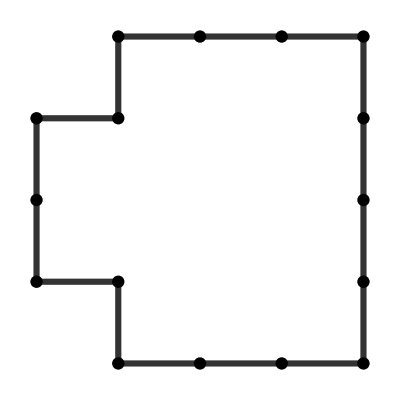

```mathematica
showCC2D[thinExhaustive[cc2]]
```